##### Пример №12.214

Разложить функцию в ряд по степеням z :

f(z)=e^(-z^2)

Рассмотрим сначала решение данной задачи “в лоб”. Так как данная нам функция аналитична во всей комплексной плоскости, то для разложения функции в ряд применима формула (8).

Запишем заданную функцию:

```mathematica
f[z_]:=Exp[-z^2]
```

Теперь запишем выражение для n-ого коэффициента с_n:

```mathematica
c[n_]:=D[f[z],{z,n}]/n!/.z->0
```

Так как мы вычисляем разложение в ряд Тейлора в окрестности точки 0, то z_0=0. Такой ряд также называют рядом Маклорена.

Для того чтобы получить окончательный ответ, найдем сумму ряда, например до 8 члена:

```mathematica
Sum[c[n] z^n,{n,0,8}]
```

1-z^2+z^4/2-z^6/6+z^8/24

Запишем данное выражение в виде функции:

```mathematica
r[z_,k_]:=Sum[c[n] z^n,{n,0,k}]
```

Для того чтобы проверить полученный результат, построим графики функции для исходной функции и ряда до 16 члена:

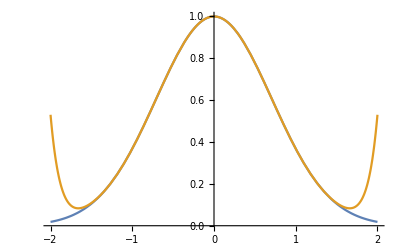

```mathematica
Plot[{f[z],Evaluate@r[z,16]},{z,-2,2},PlotRange->All]
```

Примечание: функция Evaluate здесь используется для того, чтобы сначала получить разложение в ряд Тейлора, а затем в него происходила подстановка значений z отрезка [-2;2].

Увеличивая максимальный порядок разложения, можно добиться сходимости ряда к функции на более широком отрезке.

##### Програмный модуль

Составим учебную программу, которая будет выполнять разложение функции в ряд Тейлора по формуле (8).

Имеем следующую тривиальную последовательность действий:

Пусть задана функция f(z)=cos(z).

```mathematica
f[z_]:=Cos[z]
```

1. Записываем функцию коэффициента:

```mathematica
c[n_,z0_]:=D[f[z],{z,n}]/n!/.z->z0
```

2. Находим сумму:

```mathematica
Sum[c[n,0](z-0)^n,{n,0,8}]
```

1-z^2/2+z^4/24-z^6/720+z^8/40320

Соберем это всё в единый модуль:

```mathematica
seriesO[func_,z_,z0_,k_]:=Module[{coef},
coef[n_]:=D[func,{z,n}]/n!/.z->z0;
Sum[coef[n](z-z0)^n,{n,0,k}]]
```

Продемонстрируем пример:

##### Пример №12.215

```mathematica
seriesO[Sin[z]^2,z,0,12]
```

z^2-z^4/3+(2 z^6)/45-z^8/315+(2 z^10)/14175-(2 z^12)/467775

##### Пример №12.242

```mathematica
seriesO[Exp[z^2-4z+1],z,2,12]
```

1/ⅇ^3+(-2+z)^2/ⅇ^3+(-2+z)^4/(2 ⅇ^3)+(-2+z)^6/(6 ⅇ^3)+(-2+z)^8/(24 ⅇ^3)+(-2+z)^10/(120 ⅇ^3)+(-2+z)^12/(720 ⅇ^3)

Напомним, что данный модуль использует формулу (8) для разложения функции в ряд.

Рассмотрим другие пути решения поставленной задачи.

##### Пример №12.231

Используя разложения основных элементарных функций, разложить функцию в ряд по степеням z и указать область сходимости полученного ряда:

f(z)=∫_0^z e^(-t^2/2)ⅆt

На этот раз воспользуемся стандартными разложениями (9)-(15), для того чтобы получить разложение функции в ряд.

Подынтегральная функция - эскпоненциальная, значит используя выражение (9), а также замену h=-t^2/2, получим:

```mathematica
seriesO[Exp[h],h,0,8]/.h->-t^2/2
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080-t^14/645120+t^16/10321920

Теперь требуется лишь проинтегрировать полученное выражение:

```mathematica
Integrate[seriesO[Exp[h],h,0,8]/.h->-t^2/2,{t,0,z}]
```

z-z^3/6+z^5/40-z^7/336+z^9/3456-z^11/42240+z^13/599040-z^15/9676800+z^17/175472640

Получили разложение в ряд Тейлора до 17ого члена исходной функции, причем, так как область сходимости ряда (9) - вся комплексная плоскость, то и областью сходимости полученного ряда также является вся комплексная плоскость.

Примечание: если слегка модифицировать модуль, полученный в предыдущем примере:

```mathematica
seriesO1[func_,z_,z0_,k_]:=Module[{coef,t},
coef[n_]:=D[func[t],{t,n}]/n!/.t->z0;
Sum[coef[n](z-z0)^n,{n,0,k}]]
```

Если записать функцию при помощи безымянной переменной (см. Help -> Slot), например:

```mathematica
f=Exp[#]&;
```

```mathematica
f[z]
```

ⅇ^z

То, получим следующий результат:

```mathematica
seriesO1[Exp[#]&,-t^2/2,0,8]
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080-t^14/645120+t^16/10321920

```mathematica
Integrate[seriesO1[Exp[#]&,-t^2/2,0,8],{t,0,z}]
```

z-z^3/6+z^5/40-z^7/336+z^9/3456-z^11/42240+z^13/599040-z^15/9676800+z^17/175472640

Также вместо безымянной функции, можно использовать просто заголовок подынтегральной функции:

```mathematica
seriesO1[Exp,-t^2/2,0,8]
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080-t^14/645120+t^16/10321920

##### Пример №12.218

Используя разложения основных элементарных функций, разложить функцию в ряд по степеням z и указать область сходимости полученного ряда:

f(z)=(27-z)^(1/3)

Преобразуем выражение:

f(z)=3(1-z/27)^(1/3)

Теперь, пользуясь стандартным разложением (14), при помощи замены t=-z/27, найдем разложение исходной функции в ряд:

При помощи безымянной функции:

```mathematica
seriesO1[3(1+#)^(1/3)&,-z/27,0,6]
```

3-z/27-z^2/2187-(5 z^3)/531441-(10 z^4)/43046721-(22 z^5)/3486784401-(154 z^6)/847288609443

При помощи замены:

```mathematica
seriesO[3(1+t)^(1/3),t,0,6]/.t->-z/27
```

3-z/27-z^2/2187-(5 z^3)/531441-(10 z^4)/43046721-(22 z^5)/3486784401-(154 z^6)/847288609443

Область сходимости ряда определим из:

|t|<1 ⟹|z|<27